```mathematica
(* Aer E 451 PS7 Problem 4 *)

ClearAll["Global`*"]
```

```mathematica
tmax=5;
g:=9.81
l:=.300
rg:=.400
nd2:=NDSolve[{ϕ''[t]==-(g l)/rg^2 Sin[ϕ[t]],ϕ[0]==π/2,ϕ'[0]==0},{ϕ},{t,0,tmax}]
```

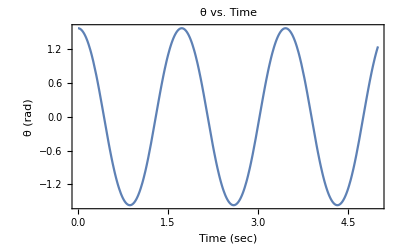

```mathematica
Plot[Evaluate[ϕ[t]/.nd2],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ (rad)"},PlotLabel-> Style["θ vs. Time",14]]
```

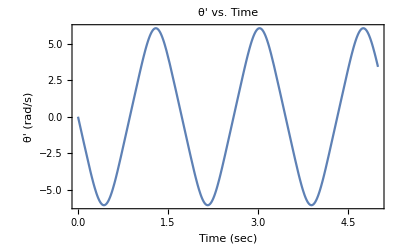

```mathematica
Plot[Evaluate[ϕ'[t]/.nd2],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ' (rad/s)"},PlotLabel-> Style["θ' vs. Time",14]]
```

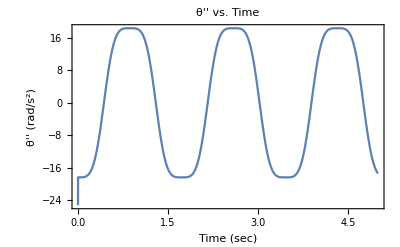

```mathematica
Plot[Evaluate[ϕ''[t]/.nd2],{t,0,tmax},Frame->{True,True},FrameLabel->{"Time (sec)","θ'' (rad/s^2)"},PlotLabel-> Style["θ'' vs. Time",14]]
```